```mathematica
Eigenvalues[{{0,1,0,0},{0,0,1,0},{0,0,0,1},{(-2 + 12 z^2 )/b,0,1/b,0}}]
```

{-(√(b-b √(1-8 b+48 b z^2)))/(√2 b),(√(b-b √(1-8 b+48 b z^2)))/(√2 b),-(√(b+b √(1-8 b+48 b z^2)))/(√2 b),(√(b+b √(1-8 b+48 b z^2)))/(√2 b)}

```mathematica
Eigenvalues[{{a,b},{c,d}}]
```

{1/2 (a+d-√(a^2+4 b c-2 a d+d^2)),1/2 (a+d+√(a^2+4 b c-2 a d+d^2))}

```mathematica
ReImPlot[{ArcSin[x],ArcCos[x]},{x,-4,4}]
```

ReImPlot[{ArcSin[x],ArcCos[x]},{x,-4,4}]

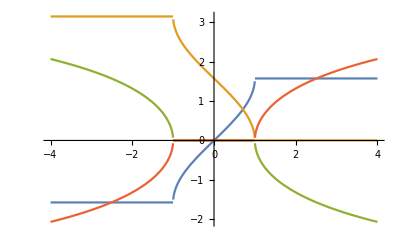

```mathematica
Plot[{Re[ArcSin[x]],Re[ArcCos[x]],Im[ArcSin[x]],Im[ArcCos[x]]},{x,-4,4}]
```

```mathematica
Eigenvalues[{{0,1},{-2 (1 + 6 u^2),0}}]
```

{-√2 √(-1-6 u^2),√2 √(-1-6 u^2)}

```mathematica
L=10;s=ParametricNDSolveValue[{y''[x]-2*y[x]+4*y0^2 y[x]^3-y''''[x]==0,y[0]==1,y'[0]==0,y''[L]==0,y'[L]==0},y,{x,0,L},{y0}]
```

ParametricFunction[<>]

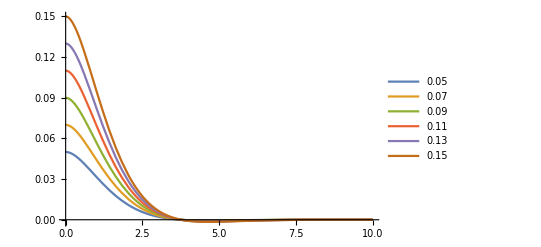

```mathematica
Plot[Evaluate[Table[y0 s[y0][x],{y0,.05,.15,.02}]],{x,0,L},PlotRange->All,PlotLegends->Table[y0,{y0,.05,.15,.02}]]
```

```mathematica
s=NDSolve[{y''[x]-2*y[x]+4*y[x]^3-y''''[x]==0,y[0]==1,y'[0]==0,y''[L]==0,y'[L]==0},y,{x,0,10},WorkingPrecision->30, MaxSteps->10000]
```

$Aborted

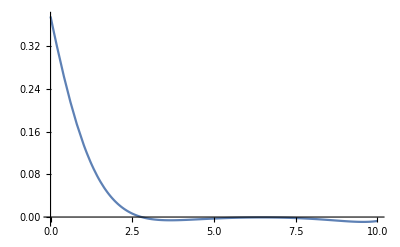

```mathematica
Plot[Evaluate[y[x]/.s],{x,0,10},PlotRange->All]
```